## Krasovskii example, Problem 2.17

```mathematica
a=({{-2, 1}, {1, -4-3 x^2}});
```

```mathematica
eigs=Eigenvalues[a];  TraditionalForm[eigs]
```

{1/2 (-3 x^2-√(9 x^4+12 x^2+8)-6),1/2 (-3 x^2+√(9 x^4+12 x^2+8)-6)}

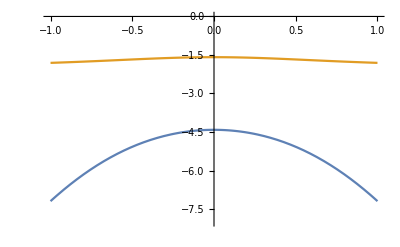

```mathematica
Plot[eigs,{x,-1,1},PlotRange->{-8,0}]  (* direct check that eigenvalues < 0 *)
```

```mathematica
tend=5;
{xsol1,xsol2}=NDSolveValue[{x1'[t]==-2x1[t]+x2[t],x2'[t]==x1[t]-2x2[t]-x2[t]^3,x1[0]==1,x2[0]==0},{x1,x2},{t,0,tend}];
```

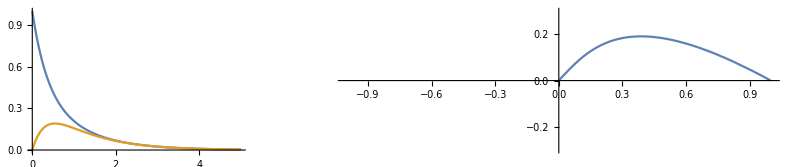

```mathematica
p1=Plot[{xsol1[t],xsol2[t]},{t,0,tend},PlotRange->All];p2=ParametricPlot[{xsol1[t],xsol2[t]},{t,0,tend}, PlotRange->{{-1,1},{-0.3,0.3}}];
GraphicsRow[{p1,p2}]
```

Export data

```mathematica
(* 
SetDirectory[NotebookDirectory[]];
dt=.01;
x1t=Table[xsol1[t],{t,0,tend,dt}];
x2t=Table[xsol2[t],{t,0,tend,dt}];
Export["krasovskii.dat",Flatten/@Transpose[{x1t,x2t}],"Table"] 
*)
```